```mathematica
inside[u_]:=
Module[
{points=u},
pointy=Input["Enter a point: {x,y}"];
(*Calls polygon function from previous homework to determine if polygon is simple of not*)
message=polygon[points,pointy];

If[message==False,
Print["Not a simple polygon."],
sully=Polygon[points];(*create a reagion from the points, using the Polygon function*)
x=RegionMember[sully,pointy];(*test to determine if point is inside region*)
If[x==True,
Return["Simple Polygon, Point is inside."],
Return["Simple Polygon, Point is outside."];
]]
]
```

SetDelayed::write: Tag Integer in 0[u_] is Protected.

$Failed

```mathematica
polygon[x_,p_]:=
Module[
{list = x,
point=p},
(*to draw the last connecting line, recopy point 1 as the last point*)
AppendTo[list,list[[1]]];
(*Prints graph*)
Print[Show[
Graphics[Line[list],Axes->True,AxesOrigin->{0,0}],
Graphics[{PointSize[Large],Red,Point[{point}]}]]];
length=Length[list];

(*Outer loop, creates region from points, doesn't test the final region since that is redundant*)
For[i=1,i<length- 1,i++,
(*our region maker*)
reg1=region[list,i,i+1];

(*Inner loop, creates a second non-consequtive region and tests for a interception with the first region*)
For[j=i+1,j+2<length ,j++,
(*makes sure new region is non-consequtive*)
reg2=region[list,j+1,j+2];
(*determines if intercept exists*)
If[interceptFound[reg1,reg2],
Return[False];
]
]
];
Return[True];
];
```

```mathematica
region[list_,xe_,ye_]:=
Module[
{l=list,
x=xe,
y=ye},
(*creates region from list and list indexes*)
Return[Region[Line[{l[[x]], l[[y]]}]]]];
```

```mathematica
interceptFound[x_,y_]:=
Module[
{reg1=x,
reg2=y},
(*Because RegionDisjoint shows true for disconnected lines, we return false because they are not intercepting*)
If[RegionDisjoint[x,y],
Return[False], Return[True];
]
]
```

```mathematica
inside[{{1,1},{6,4},{1,4},{6,1},{4,8}}]
```

0[{{1,1},{6,4},{1,4},{6,1},{4,8}}]

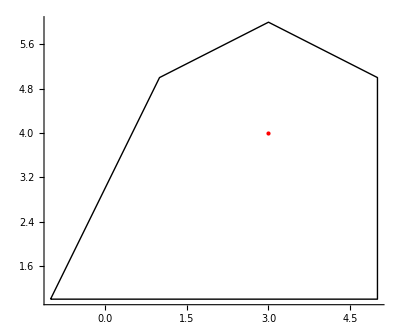

Simple Polygon, Point is inside.

```mathematica
inside[{{-1,1},{5,1},{5,5},{3,6},{1,5}}]
```

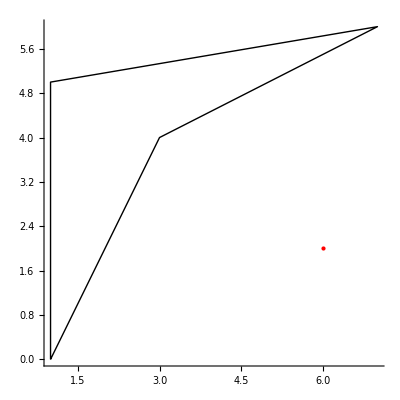

Simple Polygon, Point is outside.

```mathematica
inside[{{1,0},{1,5},{7,6},{3,4}}]
```

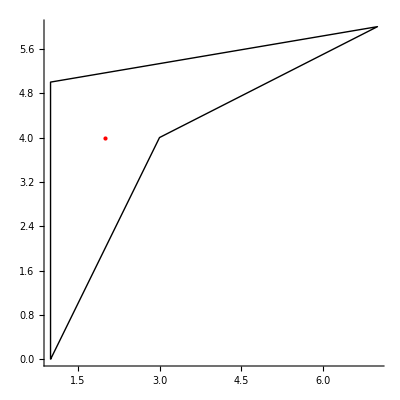

Simple Polygon, Point is inside.

```mathematica
inside[{{1,0},{1,5},{7,6},{3,4}}]
```